# Functional form harvest output vs preciptation

```mathematica
ClearAll[x,a,b,y]
```

## Coefficient functions

#### Coefficients part 1

```mathematica
a = 10.12698*z^ 0.4438413
```

10.127 z^0.443841

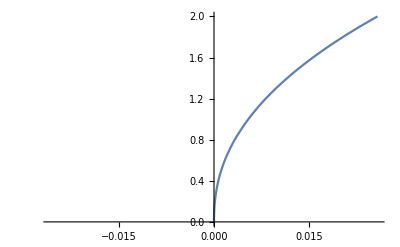

```mathematica
Plot[a,{z,-0.025872219902713604,0.025872219902713604}]
```

```mathematica
b= 0.0007185194*z-1.219122
```

-1.21912+0.000718519 z

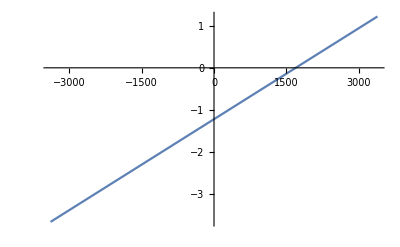

```mathematica
Plot[b,{z,-3393.4282080623016,3393.4282080623016}]
```

#### Coefficients part 2

```mathematica
c = 241.7529*z^-0.04680991
```

241.753/z^0.0468099

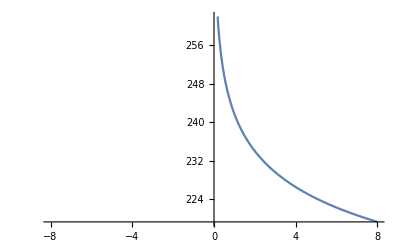

```mathematica
Plot[c,{z,-8,8}]
```

```mathematica
d=-1.017218*z^-0.09058337
```

-1.01722/z^0.0905834

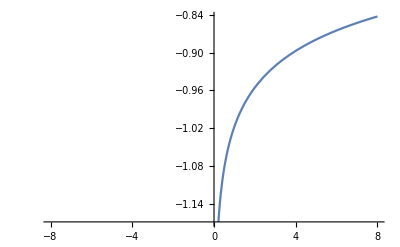

```mathematica
Plot[d,{z,-8,8}]
```

#### Where z is precipitation

## Plotting harvest output vs precipitation

```mathematica
y = a x Exp[b x]
```

10.127 ⅇ^(x (-1.21912+0.000718519 z)) x z^0.443841

```mathematica
Plot3D[y,{x,0,2},{z,0,1000}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
w =  c x Exp[d x]
```

(241.753 ⅇ^(-(1.01722 x)/z^0.0905834) x)/z^0.0468099

```mathematica
Plot3D[w,{x,0,2},{z,1000,6000}]
```

-Graphics3D-

#### Where x is LSU

## Plotting harvest output vs precipitation

```mathematica
h = If[z<880, y,w]
```

If[z<880,y,w]

```mathematica
Plot3D[h,{x,0,10},{z,0,6000}, Mesh->Full]
```

-Graphics3D-